0.48783

0.126127

0.257909

5

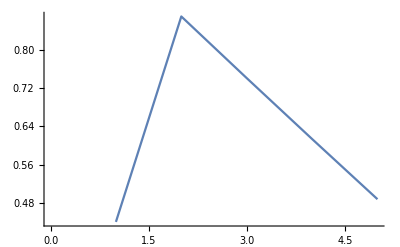

```mathematica
f[x_]:=ⅇ^-x-x;
Emin=10^-9;
Nmax=4;
Iteraciones=0;
Bandera=0;
Datos={};

While [Bandera==0,
Xizq=Input["Introduce Xizq"];
Xder=Input["Introduce Xder"];
If[f[Xizq]*f[Xder]≤0,Bandera=1, Bandera=0];

If[f[Xizq]==0,Print[Xizq],Error=0,(*No se hace nada*)];
If[f[Xder]==0,Print[Xder],Error=0,(*No se hace nada*)];
          ]

If[Xder==0,Xder=Emin,Xder=Xder];
Error=Abs[(Xder-Xizq)/Xder];


While[((Error>Emin) && (Iteraciones≤Nmax) && (Bandera==1)),
Xant=Xder;
Xact1=(Xder+Xizq)/2;
Xact=Xact1-(f[Xact1](Xact1-Xizq))/(f[Xizq]-f[Xact1]);
AppendTo[Datos,Xact];
If[f[Xact]*f[Xder]<0,Xizq=Xact,Xder=Xact];
If[Xact==0,Xact=Emin,Xact=Xact];
Error=Abs[(Xact-Xant)/Xact];
If[f[Xact]==0,Error=0,Error=Error];

Iteraciones++;
Xant=Xact;
            ]

Xact//N
f[Xact]//N
Error//N
Iteraciones
ListPlot[Datos,Joined->True,PlotRange->All](*No evaluar con muchas iteraciones*)
(*Nmax de 4 si no tarda demasiado*)
```